```mathematica
<<NeoHookean`
```

```mathematica
ss[u_,v_,ϵ_]:=(u+√(v^2+u^2 ϵ-v^2 ϵ))/(u^2-v^2);
sss[ux_,uy_]:=-(ux+uy+√((ux-uy)^2+4 ux uy ϵ))/(2 ux uy);
InvertibleNeoHookeanPotential[σx_,σy_,λ_,μ_,ϵ_:0.2]:=Module[{qx,qy,u,ux,uy,s,d,h,hu},
If[σx σy≥ ϵ&&σx>0,
NeoHookeanPotential[σx,σy,λ,μ]
,
{ux,uy}={-1+σx,-1+σy};
If[ux^2<0.0000001,
s=(ϵ-1)/(-1+σy);
{qx,qy}={1,ϵ};
,
If[uy^2 < 0.0000001,
s=(ϵ-1)/(-1+σx);
{qx,qy}={ϵ,1};
,
s=-(-2+σx+√((σx-σy)^2+4 ϵ (-1+σx) (-1+σy))+σy)/(2(-1+σy)(-1+σx));
{qx,qy}={1,1}+s{-1+σx,-1+σy};
]
];
hu={1-σx,1-σy}(s-1);
(* Intersection Point between state vector and ϵ line *)
NeoHookeanPotential[qx, qy,λ,μ]+

hu.{((-1+qx^2) μ+λ Log[qx qy])/qx,((-1+qy^2) μ+λ Log[qx qy])/qy}+
(hu).{{(λ+μ+qx^2 μ-λ Log[qx qy])/qx^2,λ/(qx qy)},{λ/(qx qy),(λ+μ+qy^2 μ-λ Log[qx qy])/qy^2}}.(hu)/2
]
]
```

```mathematica
trans = {σx-> 1+ux,σy->1+uy};
extrapolate=Block[{qx,qy,hu},
{qx,qy}={1,1}+s{-1+σx,-1+σy};
hu={1-σx,1-σy}(s-1);
NeoHookeanPotential[qx, qy,λ,μ]+

hu.{((-1+qx^2) μ+λ Log[qx qy])/qx,((-1+qy^2) μ+λ Log[qx qy])/qy}+
(hu).{{(λ+μ+qx^2 μ-λ Log[qx qy])/qx^2,λ/(qx qy)},{λ/(qx qy),(λ+μ+qy^2 μ-λ Log[qx qy])/qy^2}}.(hu)/2
];
expr=FullSimplify[extrapolate/.trans]/.srules//FullSimplify
```

```mathematica
javaFileString = 
"package physics;
import static java.lang.Math.sqrt;
import static java.lang.Math.log;
import static java.lang.Math.signum;
import static java.lang.Math.abs;

public class InvertibleNeoHookeanStressDensity {
	final static double square(double x) {
		return x*x;
	}
	final static double cube(double x) {
		return x*x*x;
	}
	final static double quart(double x) {
		return x*x*x*x;
	}
	final static public double[] computeStressDifferentialComponents(
							double sx, double sy, double l, 
							double mu, double eps) 
	{
		double ux = sx - 1;
		double uy = sy - 1;
		double ux2 = ux*ux;
		double ux3 = ux2*ux;
		double ux4 = ux2*ux2;
		double ux5 = ux3*ux2;
		double uy2 = uy*uy;
		double uy3 = uy2*uy;
		double uy4 = uy2*uy2;
		double vx = sx+1;
		double vx2 = vx*vx;
		double vx3 = vx2*vx;
		double vy = sy+1;
		double vy2 = vy*vy;
		double vy3 = vy2*vy;
		double vy4 = vy2*vy2;
		double sy2 = sy*sy;
		double sx2 = sx*sx;
		double eps2 = eps*eps;
		double inveps2 = 1/eps2;
		double delta = eps-1;
		double delta2 = delta*delta;
		double delta3 = delta2*delta;
		double c0 = square(ux+uy);
		double c1 = c0+4*ux*uy*delta;
		assert c1 > 0;
		assert sx + sy >= 0; // IFE Convention
		double lEps = Math.log(eps);
		double k = mu -(-l+l*lEps);
		double bEps = Math.sqrt(c1);
		double d = 2*bEps*ux2*uy2*eps2;
		double psi0=0, f1=0, f2=0, psi11=0, psi12=0, psi22=0;
		
		<eval>
		
		return new double[] {psi0, f1, f2, psi11, psi12, psi22};
	}

	final static public double[] computeStressGradientComponents(
							double sx, double sy, double l, 
							double mu, double eps) 
	{
		double ux = sx - 1;
		double uy = sy - 1;
		double ux2 = ux*ux;
		double ux3 = ux2*ux;
		double ux4 = ux2*ux2;
		double uy2 = uy*uy;
		double uy3 = uy2*uy;
		double uy4 = uy2*uy2;
		double vx = sx+1;
		double vy = sy+1;
		double eps2 = eps*eps;
		double inveps2 = 1/eps2;
		double delta = eps-1;
		double delta2 = delta*delta;
		double c0 = square(ux+uy);
		double c1 = c0+4*ux*uy*delta;
		assert c1 > 0;
		assert sx + sy >= 0; // IFE Convention
		double lEps = Math.log(eps);
		double k = mu -(-l+l*lEps);
		double bEps = Math.sqrt(c1);
		double d = 2*bEps*ux2*uy2*eps2;
		double psi0=0, psi1=0, psi2=0;
		
		<eval2>
		
		return new double[] {psi0, psi1, psi2};
	}
}
";
testLimitsString="
		if(Math.abs(ux) < 1e-10) {
			<uxlimit>
		} else if (Math.abs(uy) < 1e-10) {
			<uylimit>
		} else {
			<general>
		}
		";
```

```mathematica
isPositive = #>1&;
isNegative = #<-1&;
exprString[j_,psiexprs_,psilimitexprs_,cond_]:=
Module[{i=j,
subst={
(ux+uy)^2+4 ux uy δ->c1,
Log[1+δ]->lEps,
lϵ->lEps,
bϵ-> bEps,
ϵ->eps,
(1+δ)^(i_?isPositive):> ToExpression["eps"<>ToString[i]],
(1+δ)^(i_?isNegative):> 1/ToExpression["eps"<>ToString[-i]],
1+δ->eps,
eps2^-1->inveps2,
δ-> delta,
δ^2-> delta2,
δ^3->delta3,
λ->l,
ux^(i_?isPositive):> ToExpression["ux"<>ToString[i]],
uy^(i_?isPositive):> ToExpression["uy"<>ToString[i]],
ux^(i_?isNegative):> 1/ToExpression["ux"<>ToString[-i]],
uy^(i_?isNegative):> 1/ToExpression["uy"<>ToString[-i]],
2+ux+uy->sx+sy,
(2+ux)^4->vx4,
(2+uy)^4->vy4,
(2+ux)^3->vx3,
(2+uy)^3->vy3,
(2+ux)^2->vx2,
(2+uy)^2->vy2,
(1+ux)^2->sx2,
(1+uy)^2->sy2,
(1+ux)->sx,
(1+uy)->sy,
(2+ux)->vx,
(2+uy)->vy,
cube[vx]->vx3,
cube[vy]->vy3,
square[ux+uy]->c0,
square[eps]->eps,
x_^2:>  square[x],
x_^-2:>  1/square[x],
x_^3:>  cube[x],
x_^-3:>  1/cube[x],
x_^4:>  quart[x],
x_^-4:>  1/quart[x],
Sign->signum,
Abs->abs
}
},
StringReplace[testLimitsString,
{"<general>"-> (ToString[Keys[psiexprs][[i]]]<>" = " <> cond[i] <>
StringReplace[ToString[Values[psiexprs][[i]]2 bϵ ux^2 uy^2 (1+δ)^2 /d//.subst
,InputForm,PageWidth->70] ,"\n"->"\n\t\t\t"]<> ";"),
"<uxlimit>"-> (ToString[Keys[psiexprs][[i]]]<>" = " <> cond[i]<>
StringReplace[ToString[psilimitexprs[[i,1]]//.subst
,InputForm,PageWidth->70] ,"\n"->"\n\t\t\t"]<> ";"),
"<uylimit>"-> (ToString[Keys[psiexprs][[i]]]<>" = " <> cond[i] <>
StringReplace[ToString[psilimitexprs[[i,2]]//.subst
,InputForm,PageWidth->70] ,"\n"->"\n\t\t\t"]<> ";\n\t\t")
}]
]
SetDirectory[NotebookDirectory[]]
file=OpenWrite["../src/main/java/physics/InvertibleNeoHookeanStressDensity.java"]
WriteString[file,
StringReplace[javaFileString, {
"<eval>"-> 
StringJoin[StringReplace[exprString[#,psiexprs,psilimitexprs,
Which[#==2," (sx+sy<1e-10)?(1e10):",#==3,"(sx+sy<1e-10)?(-1e10):",True,""]&],{"["->"(","]"->")"}]&/@Range[1,6]],
"<eval2>"-> 
StringJoin[StringReplace[exprString[#,psiexprs2,psilimitexprs2,""&],{"["->"(","]"->")"}]&/@Range[1,3]]
}
]
]
Close[file]
```

/home/eduard/programming/Evolutionary/scripts

OutputStream[…]

../src/main/java/physics/InvertibleNeoHookeanStressDensity.java

```mathematica
neoh=1/2 (μ (-2+σx^2+σy^2)-2 μ Log[σx σy]+λ Log[σx σy]^2);
psiexprsneo={
psi0-> neoh,
f1-> (σy D[neoh,σx]-σx D[neoh,σy])/(σx^2-σy^2),
f2-> (σx D[neoh,σx]-σy D[neoh,σy])/(σx^2-σy^2),
psi11->  D[neoh,σx,σx],
psi12->  D[neoh,σx,σy],
psi22->  D[neoh,σy,σy]
}//FullSimplify
```

{psi0→1/2 (μ (-2+σx^2+σy^2)-2 μ Log[σx σy]+λ Log[σx σy]^2),f1→(μ-λ Log[σx σy])/(σx σy),f2→μ,psi11→(λ+μ+μ σx^2-λ Log[σx σy])/σx^2,psi12→λ/(σx σy),psi22→(λ+μ+μ σy^2-λ Log[σx σy])/σy^2}

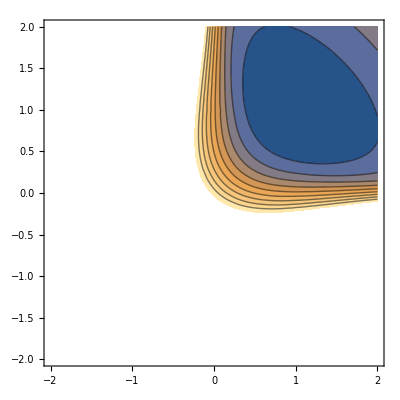

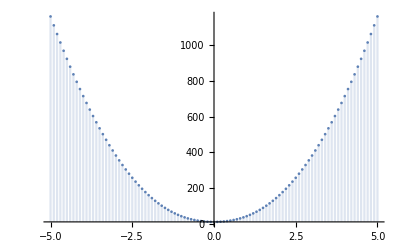
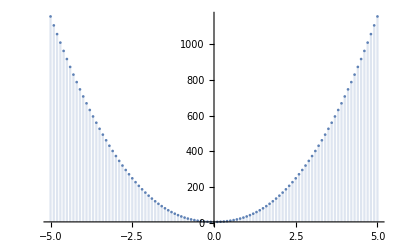
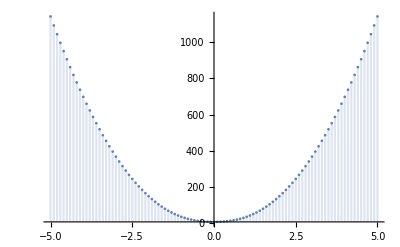
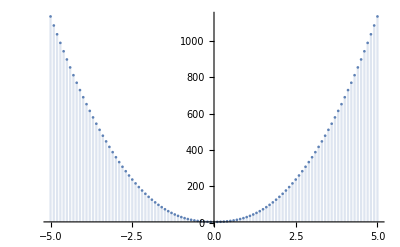
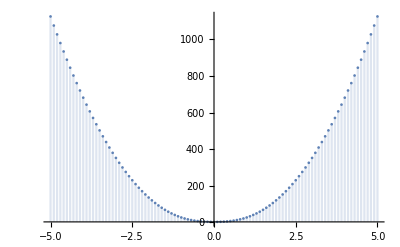
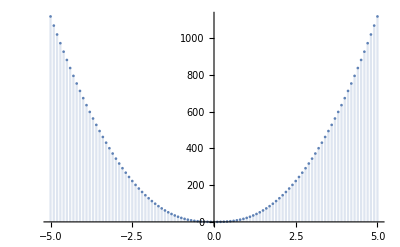
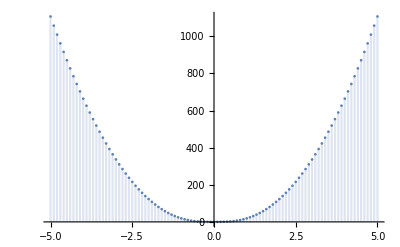

```mathematica
Block[{f,i=1},
f[σx_,σy_]=Evaluate[
Which[
σx σy>ϵ&&σx>0,Evaluate[Values[psiexprsneo][[i]]],
Abs[ux]<10^-10,Evaluate[psilimitexprs[[i,1]]],
Abs[uy]<10^-10,Evaluate[psilimitexprs[[i,2]]],
True,Evaluate[Values[psiexprs][[i]]]
]//.{lϵ-> Log[ϵ],δ-> -1+ϵ,k-> μ-(-λ+λ lϵ),ϵ->0.3,μ->1,λ->1,bϵ-> ((ux+uy)^2+4 ux uy δ)^(1/2),ux->σx-1,uy->σy-1}];
Print@ContourPlot[f[σx,σy],{σx,-2,2},{σy,-2,2},PlotRange->{0,10},Exclusions->None];
Print@Table[DiscretePlot[f[k+σx,k+-σx],{σx,-5,5,0.1},PlotRange->Full],{k,0,1,0.1}];
]
```

```mathematica
Block[{f},
f[σx_,σy_]=Evaluate[
Which[
σx σy>ϵ&&σx>0,Evaluate[Values[psiexprsneo]],
Abs[ux]<10^-10,Evaluate[{psilimitexprs[[All,1]],psilimitexprs2[[All,1]]}],
Abs[uy]<10^-10,Evaluate@{psilimitexprs[[All,2]],psilimitexprs2[[All,2]]},
True,Evaluate@{Values[psiexprs],Values[psiexprs2]}
]//.{lϵ-> Log[ϵ],δ-> -1+ϵ,k-> μ-(-λ+λ lϵ),ϵ->0.3,μ->1.2,λ->1.3,
bϵ-> ((ux+uy)^2+4 ux uy δ)^(1/2),ux->σx-1,uy->σy-1}];
Print@NumberForm[f[0.3,0.5],15];
Print@NumberForm[f[1,0.2],15];
Print@NumberForm[f[0.2,1],15];
Print@NumberForm[f[0.01,0.002],15];
Print@NumberForm[f[-0.02,0.02],15];
]
```

{{3.44706684599153,18.7689664089106,0.0816001282036203,24.5276960027332,-0.448611202750378,14.0356565981633},{3.44706684599153,-9.36000316599424,-5.58988985857141}}

{{2.9585392278565,13.7223024624783,1.14118685408538,3.83247641114176,-3.07712305191825,46.3684960624857},{2.9585392278565,-1.60327363841031,-13.494065091661}}

{{2.9585392278565,13.7223024624782,1.14118685408533,46.3684960624857,-3.07712305191825,3.83247641114176},{2.9585392278565,-13.494065091661,-1.60327363841031}}

{{11.9055855463672,1244.84315670161,-1210.09421816975,26.7939884373991,-7.83297749968835,27.0390187815828},{11.9055855463672,-14.5906284951007,-14.8686200033555}}

{{12.096443131052,ComplexInfinity,ComplexInfinity,27.6203475133729,-7.93830358922197,26.4064283369386},{12.096443131052,-15.5487202819036,-14.1511871090737}}

```mathematica
psiexprs={
psi0-> 1/(4 ux^2 uy^2 (1+δ)^2)(k (uy^4+2 ux uy^3 (2+uy+3 δ)+bϵ (ux+uy+2 ux uy) ((ux+uy)^2+4 ux uy δ)+2 ux^2 uy^2 (3+uy (3+2 uy)+8 δ+2 uy (3+uy) δ+(6+uy (2+uy)) δ^2)+2 ux^3 uy (2+3 δ+uy (3+2 δ (3+uy+δ)))+ux^4 (1+2 uy (1+uy (2+δ (2+δ)))))-2 ux^2 uy^2 (1+δ) ((ux-uy)^2+(2+ux (2+ux)+uy (2+uy)) δ) λ-2 ux^2 uy^2 (1+δ)^2 Log[1+δ] (2 k-(2+ux (2+ux)+uy (2+uy)) λ+λ Log[1+δ])),
f1-> (k ((ux+uy)^2+4 ux uy δ) (ux^4 (1+uy)+uy^3 (1+uy)+ux uy^2 (3+δ+uy (3+uy+δ))+ux^3 (1+uy (3+δ-2 uy δ))+ux^2 uy (3+δ-2 uy (-2+δ+uy δ)))+bϵ (k (ux^5 (1+uy)+uy^4 (1+uy)+ux uy^3 ((2+uy)^2+3 (1+uy) δ)+ux^2 uy^2 (6+7 uy+uy^2+3 (2+uy) δ)+ux^4 (1+uy (4+uy+3 δ-2 uy^2 δ))+ux^3 uy (4+3 δ+uy (7+4 uy+3 δ-2 uy (2+uy) δ)))-2 ux^3 uy^3 (2+ux+uy) (1+δ) λ))/(2 bϵ ux^3 uy^3 (2+ux+uy) (1+δ)^2),f2-> (k (ux+uy) ((ux+uy)^2+4 ux uy δ) (uy^2+ux^2 (1+3 uy (1+uy))+ux uy (2+3 uy+δ))+bϵ (k (uy^4+3 ux^2 uy^2 (1+uy) (2+uy+2 δ)+ux uy^3 (4+3 uy+3 δ)+ux^3 uy (4+3 δ+uy (9+6 δ+2 uy (5+2 δ (2+δ)+uy (2+δ (2+δ)))))+ux^4 (1+uy (3+uy (3+2 uy (2+δ (2+δ))))))+2 (-1+lϵ) ux^3 uy^3 (2+ux+uy) (1+δ)^2 λ))/(2 bϵ ux^3 uy^3 (2+ux+uy) (1+δ)^2),
psi11-> 1/(2 bϵ ux^4 uy^2 (1+δ)^2)(k (3 uy^4 (bϵ+uy)+ux^5 (1+2 uy)-2 ux^3 uy^2 (1+2 uy) δ (1+δ)+2 ux^2 uy^3 (2+uy+2 uy δ+δ (4+3 δ))+ux uy^3 (2 bϵ (2+uy+3 δ)+uy (7+2 uy+12 δ))+ux^4 (bϵ+uy (1+2 bϵ+2 δ+2 uy (1+2 δ+bϵ (2+δ (2+δ))))))-2 bϵ ux^4 uy^2 (1+δ)^2 λ+2 bϵ ux^4 uy^2 (1+δ)^2 λ Log[1+δ]),psi12-> 1/(2 bϵ ux^3 uy^3 (1+δ)^2)(-k (2 ux^5 (1+uy)+2 uy^4 (bϵ+uy)+ux^2 uy^3 (2+δ (3+2 δ)+uy (2+4 δ))+ux uy^3 (bϵ (2+2 uy+3 δ)+uy (4+2 uy+7 δ))+ux^3 uy (-2 uy^2 δ (2+bϵ+2 δ)+bϵ (2+3 δ)+uy (2+δ (3+2 δ)))+ux^4 (2 bϵ (1+uy)+uy (4+7 δ+uy (2+4 δ))))+2 bϵ ux^3 uy^3 (1+δ) λ),psi22-> 1/(2 bϵ ux^2 uy^4 (1+δ)^2)(k (uy^4 (bϵ+uy)+ux^5 (3+2 uy)+ux uy^4 (1+2 bϵ+2 uy+2 δ)+ux^4 (3 bϵ+uy (7+2 bϵ+2 uy+4 (3+uy) δ))+2 ux^3 uy (bϵ (2+3 δ)+uy (2+δ (4+3 δ-2 uy (1+δ))))+2 ux^2 uy^3 (-δ (1+δ)+uy (1+2 δ+bϵ (2+δ (2+δ)))))-2 bϵ ux^2 uy^4 (1+δ)^2 λ+2 bϵ ux^2 uy^4 (1+δ)^2 λ Log[1+δ])};
Hold[
psilimitexprs=(Table[Sum[Limit[D[1/(i!)u^i Select[Apart[#/.psiexprs,u],MemberQ[#,u^-i]& ]/.{bϵ->((ux+uy)^2+4 ux uy δ)^(1/2)},{u,i}],u->0]
,{i,1,4}]+Select[Apart[#/.psiexprs,u],Not[MemberQ[#,u|u^_]]& ]
,{u,{ux,uy}}]
)/.Log[1+δ]->lϵ&/@{psi0,f1,f2,psi11,psi12,psi22};
psilimitexprs=FullSimplify[psilimitexprs,_ ∈ Reals];
];
psilimitexprs={{1/(4 uy (1+δ)^2)Sign[uy] (k uy (3+2 uy+4 (2+uy) δ+6 δ^2)+(bϵ k (3+4 δ+uy (4+8 δ))+2 uy (k (3+uy (3+2 uy)+8 δ+2 uy (3+uy) δ+(6+uy (2+uy)) δ^2-2 lϵ (1+δ)^2)-(1+δ) (uy^2+(2+uy (2+uy)) δ+lϵ^2 (1+δ)-lϵ (2+uy (2+uy)) (1+δ)) λ)) Sign[uy]),1/(4 ux (1+δ)^2)Sign[ux] (k ux (3+2 ux+4 (2+ux) δ+6 δ^2)+(bϵ k (3+4 δ+ux (4+8 δ))+2 ux (k (3+ux (3+2 ux)+8 δ+2 ux (3+ux) δ+(6+ux (2+ux)) δ^2-2 lϵ (1+δ)^2)-(1+δ) (ux^2+(2+ux (2+ux)) δ+lϵ^2 (1+δ)-lϵ (2+ux (2+ux)) (1+δ)) λ)) Sign[ux])},{(Sign[uy] (bϵ k uy (2+ux+uy) (-uy (44+3 uy (9+2 uy))+uy (-74-31 uy+2 uy^3) δ+2 (-8+uy^2 (3+uy) (4+uy)) δ^2+2 (1+uy) (2+uy)^2 δ^3-24 (1+2 δ))-(k (uy (-uy (80+uy (192+uy (162+uy (58+7 uy))))-bϵ (32+uy (80+uy (96+uy (67+uy (25+4 uy)))))+(2+uy) (uy (1+uy) (-60+uy (-26+uy (13+8 uy)))+bϵ (-12+uy (-12+uy (2+uy) (5+2 uy (4+uy))))) δ+4 uy (2+uy)^2 (-2+uy (4+uy (7+2 uy))) δ^2)+ux (2+uy)^3 (-2+bϵ (1-uy-3 uy δ+2 uy^3 δ)+uy (-2+5 δ+uy (-7+δ (-3-4 δ+8 uy (1+δ))))))+2 bϵ uy^3 (2+uy)^3 (2+ux+uy) (1+δ) λ) Sign[uy]))/(2 bϵ uy^3 (2+uy)^3 (2+ux+uy) (1+δ)^2),((bϵ k ux (2+ux+uy) (-ux (44+3 ux (9+2 ux))+ux (-74-31 ux+2 ux^3) δ+2 (-8+ux^2 (3+ux) (4+ux)) δ^2+2 (1+ux) (2+ux)^2 δ^3-24 (1+2 δ))-1/Sign[ux](k (-ux^2 (80+ux (192+ux (162+ux (58+7 ux))))-(2+ux)^3 (2+ux (2+7 ux)) uy+ux (2+ux) (ux (1+ux) (-60+ux (-26+ux (13+8 ux)))+(2+ux)^2 (5+ux (-3+8 ux)) uy) δ+4 ux^2 (2+ux)^2 (-2 (1+uy)+ux (4+3 uy+ux (7+2 ux+2 uy))) δ^2)+bϵ (k (-ux (32+ux (80+ux (96+ux (67+ux (25+4 ux)))))-(-1+ux) (2+ux)^3 uy+ux (2+ux) (-12 (1+uy)+ux (-12 (1+uy)+ux (5+2 ux (4+ux)) (2+ux+uy))) δ)+2 ux^3 (2+ux)^3 (2+ux+uy) (1+δ) λ))) Sign[ux])/(2 bϵ ux^3 (2+ux)^3 (2+ux+uy) (1+δ)^2)},{(-k (2+uy)^4 (2+ux+uy) (1+3 uy (1+uy))+4 k uy (2+uy)^3 (2+ux+uy) (1+3 uy (1+uy)) δ+k uy (2+uy)^3 (2+ux+uy) (5+3 uy (4+3 uy)+δ)+4 k (-bϵ (1+uy)^2 (4+uy (2+uy) (2+uy (2+uy)-3 δ))-2 (4+uy (2+uy) (6+3 uy (2+uy)-δ)) (-1+uy (2+uy) δ))+bϵ k (2+uy)^3 (2+ux+uy) (1+uy (3+uy (3+2 uy (2+δ (2+δ)))))+2 bϵ (-1+lϵ) uy^3 (2+uy)^3 (2+ux+uy) (1+δ)^2 λ-bϵ k (2+ux+uy) (24+uy (52+3 uy (15+uy (6+uy)))+48 δ+uy (102+uy (89+6 uy (6+uy))) δ+2 (2+uy) (4+3 uy (2+uy)) δ^2-2 (2+uy)^2 δ^3) Abs[uy])/(2 bϵ uy^3 (2+uy)^3 (2+ux+uy) (1+δ)^2),1/2 ((9 k)/(bϵ (1+δ)^2)+k/(ux^3 (1+δ)^2)+(3 k)/(ux^2 (1+δ)^2)-(k (2+ux))/(bϵ ux^3 (1+δ)^2)+(12 k δ)/(bϵ (1+δ)^2)+(3 k (2+bϵ-ux+4 δ))/(bϵ ux (1+δ)^2)+(k (-1-3 ux+5 δ))/(bϵ ux^2 (1+δ)^2)+2 k (1+1/(1+δ)^2)+(4 k (-bϵ (1+ux)^2 (4+ux (2+ux) (2+ux (2+ux)-3 δ))-2 (4+ux (2+ux) (6+3 ux (2+ux)-δ)) (-1+ux (2+ux) δ)))/(bϵ ux^3 (2+ux)^3 (2+ux+uy) (1+δ)^2)+2 (-1+lϵ) λ-1/(ux^2 (2+ux)^3 (1+δ)^2)k (24+ux (52+3 ux (15+ux (6+ux)))+48 δ+ux (102+ux (89+6 ux (6+ux))) δ+2 (2+ux) (4+3 ux (2+ux)) δ^2-2 (2+ux)^2 δ^3) Sign[ux])},{1/(2 bϵ uy^3 (1+δ)^2)(k uy (uy+2 uy (uy+δ+2 uy δ)+bϵ (1+2 uy (1+uy (2+δ (2+δ)))))+2 bϵ (-1+lϵ) uy^3 (1+δ)^2 λ+2 bϵ k δ (1+δ) (-1+δ+3 δ^2-2 uy (1+2 δ)) Abs[uy]),1/(bϵ ux^3 (1+δ)^2)(ux^2 (k (-δ (1+δ)+ux (1+2 δ+bϵ (2+δ (2+δ))))+bϵ (-1+lϵ) ux (1+δ)^2 λ)+bϵ k (-ux+δ-2 ux δ+δ^2) Abs[ux])},{1/(2 bϵ uy^3 (1+δ)^2)(k uy (bϵ (-2+(-3+2 uy^2) δ)+uy (-2+δ (-3-2 δ+4 uy (1+δ))))+2 bϵ uy^3 (1+δ) λ+2 bϵ k δ (1+δ) (-2 uy+δ) Abs[uy]),1/(2 bϵ ux^3 (1+δ)^2)(k ux (bϵ (-2+(-3+2 ux^2) δ)+ux (-2+δ (-3-2 δ+4 ux (1+δ))))+2 bϵ ux^3 (1+δ) λ+2 bϵ k δ (1+δ) (-2 ux+δ) Abs[ux])},{1/(bϵ uy^3 (1+δ)^2)(uy^2 (k (-δ (1+δ)+uy (1+2 δ+bϵ (2+δ (2+δ))))+bϵ (-1+lϵ) uy (1+δ)^2 λ)+bϵ k (-uy+δ-2 uy δ+δ^2) Abs[uy]),1/(2 bϵ ux^3 (1+δ)^2)(k ux (ux+2 ux (ux+δ+2 ux δ)+bϵ (1+2 ux (1+ux (2+δ (2+δ)))))+2 bϵ (-1+lϵ) ux^3 (1+δ)^2 λ+2 bϵ k δ (1+δ) (-1+δ+3 δ^2-2 ux (1+2 δ)) Abs[ux])}};
```

```mathematica
psiexprs2={
psi0-> 1/(4 ux^2 uy^2 (1+δ)^2)(k (uy^4+2 ux uy^3 (2+uy+3 δ)+bϵ (ux+uy+2 ux uy) ((ux+uy)^2+4 ux uy δ)+2 ux^2 uy^2 (3+uy (3+2 uy)+8 δ+2 uy (3+uy) δ+(6+uy (2+uy)) δ^2)+2 ux^3 uy (2+3 δ+uy (3+2 δ (3+uy+δ)))+ux^4 (1+2 uy (1+uy (2+δ (2+δ)))))-2 ux^2 uy^2 (1+δ) ((ux-uy)^2+(2+ux (2+ux)+uy (2+uy)) δ) λ-2 ux^2 uy^2 (1+δ)^2 Log[1+δ] (2 k-(2+ux (2+ux)+uy (2+uy)) λ+λ Log[1+δ])),
psi1-> 1/(2 bϵ ux^3 uy^2 (1+δ)^2)(k ((ux+uy)^2+4 ux uy δ) (-uy^3+ux^3 (1+2 uy)-ux uy^2 (1+uy+δ)+ux^2 uy (1+uy+δ+2 uy δ))+bϵ k (-uy^4-ux uy^3 (2+uy+3 δ)+ux^3 uy (2+3 δ+uy (3+2 δ (3+uy+δ)))+ux^4 (1+2 uy (1+uy (2+δ (2+δ)))))-2 bϵ ux^3 uy^2 (1+δ) (ux-uy+δ+ux δ) λ+2 bϵ ux^3 (1+ux) uy^2 (1+δ)^2 λ Log[1+δ]),
psi2-> 1/(2 bϵ ux^2 uy^3 (1+δ)^2)(-k ((ux+uy)^2+4 ux uy δ) (-uy^3+ux^3 (1+uy)-ux uy^2 (1+2 uy+δ)+ux^2 uy (1-uy+δ-2 uy δ))+bϵ k (uy^4-ux^4 (1+uy)+ux uy^3 (2+2 uy+3 δ)+ux^3 uy (-2+(-3+2 uy^2) δ)+ux^2 uy^3 (3+2 δ (3+δ)+2 uy (2+δ (2+δ))))-2 bϵ ux^2 uy^3 (1+δ) (-ux+uy+δ+uy δ) λ+2 bϵ ux^2 uy^3 (1+uy) (1+δ)^2 λ Log[1+δ])
};
psilimitexprs2=(Table[Sum[Limit[D[1/(i!)u^i Select[Apart[#/.psiexprs2,u],MemberQ[#,u^-i]& ]/.{bϵ->((ux+uy)^2+4 ux uy δ)^(1/2)},{u,i}],u->0]
,{i,1,4}]+Select[Apart[#/.psiexprs2,u],Not[MemberQ[#,u|u^_]]& ]
,{u,{ux,uy}}]
)/.Log[1+δ]->lϵ&/@{psi0,psi1, psi2};
psilimitexprs2=FullSimplify[psilimitexprs2,_ ∈ Reals];
```